```mathematica
g[n_,m_]:=(n+m-1)!/(n!(m-1)!)
g[2,6]
```

21

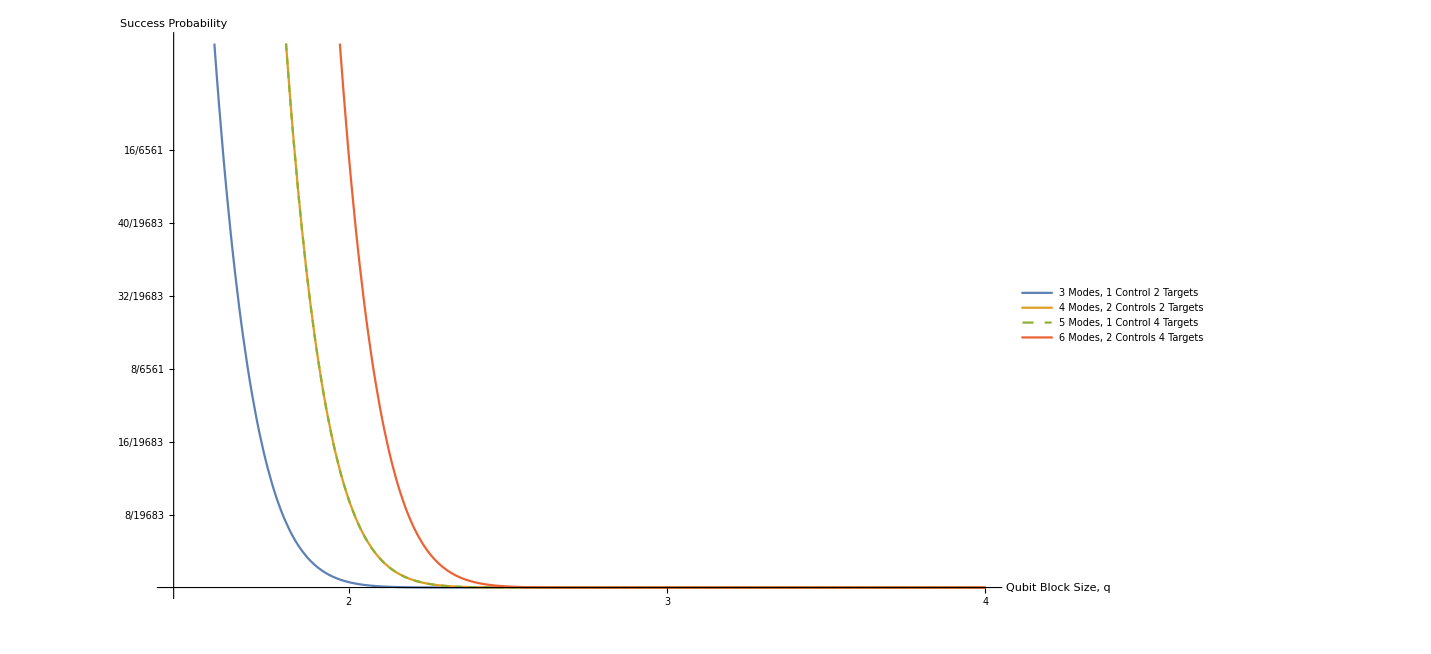

```mathematica
p1C2T[q_]:=(2/27)^(2^(2 q -2));
p2C2T[q_]:=(0.0221391)^(2^(2 q -3));
p1C4T[q_]:=(0.0221266)^(2^(2 q - 3));
p2C4T[q_]:=(0.00241264)^(2^(2 q - 4));
Plot[{p1C2T[q],p2C2T[q],p1C4T[q],p2C4T[q]},{q,1.45,4},AxesLabel->{"Qubit Block Size, q","Success Probability"},PlotLegends->Placed[{"3 Modes, 1 Control 2 Targets","4 Modes, 2 Controls 2 Targets","5 Modes, 1 Control 4 Targets","6 Modes, 2 Controls 4 Targets"},{.75,.2}],LabelStyle->{FontSize-> 20},PlotStyle->{Line,Line,Dashed},Ticks->{{1,2,3,4},{(2/27)^3,2 (2/27)^3, 3 (2/27)^3, 4 (2/27)^3, 5 (2/27)^3, 6 (2/27)^3}}]
```

```mathematica
pKLM[n_]:=(2./27)^(n (n-1) );
pBlock[n_,q_]:=(0.0023216)^((n(n-1) - n(q-1) ) 2^(2 q - 4));
pKLM[6]
pBlock[6,3]
```

1.23023×10^-34

2.17116×10^-190